### Тест 1

```mathematica
(x-0.1)(x-0.22)(x-0.55)(x-0.7)(x-0.75)
```

253.318

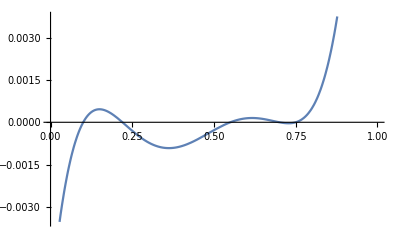

```mathematica
Plot[(x-0.1)(x-0.22)(x-0.55)(x-0.7)(x-0.75),{x,0,1}]
```

### Тест 2

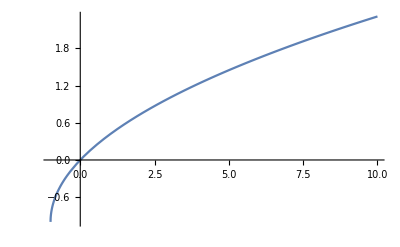

```mathematica
Plot[√(x+1)-1,{x,-1,10}]
```

```mathematica
xk = 7/2;
```

```mathematica
xk1=xk-2 √(xk+1)(√(xk+1)-1)//N
```

-1.25736

### Тест 3

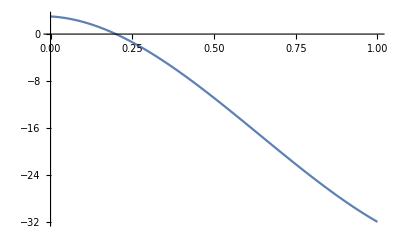

```mathematica
Plot[35 x^3-67 x^2-3x+3,{x,0,1}]
```

### Тест 4

```mathematica
{f,g} = {x^2-y^2-15,x y+4};
```

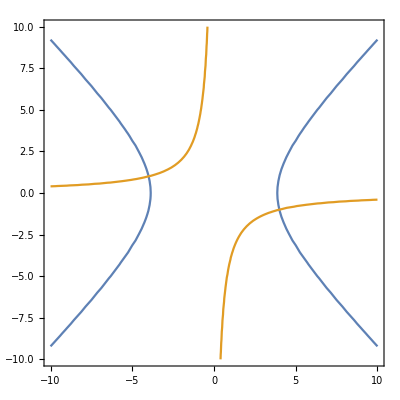

```mathematica
ContourPlot[{x^2-y^2-15==0,x y+4==0},{x,-10,10},{y,-10,10},Axes->True]
```

```mathematica
Solve[x^2-y^2-15==0&&x y+4==0,{x,y}]
```

Solve::ivar: 7/2 is not a valid variable.

Solve[False,{7/2,9/2-3/(√2)}]

### Тест 5

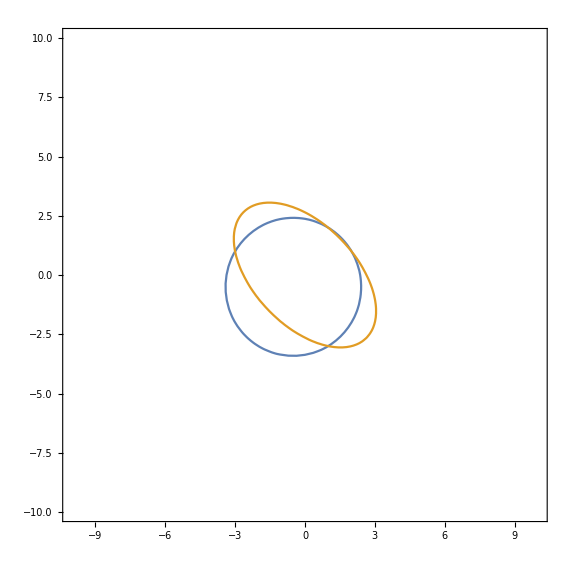

```mathematica
ContourPlot[{x^2+y^2+x+y-8==0,x^2+y^2+x y-7==0},{x,-10,10},{y,-10,10},Axes->True]
```

```mathematica
Solve[x^2+y^2+x+y-8==0&&x^2+y^2+x y-7==0,{x,y}]
```

Solve::ivar: 7/2 is not a valid variable.

Solve[False,{7/2,9/2-3/(√2)}]

Тест 5

```mathematica
f1=x^2+y^2+x+y-8;
f2=x^2+y^2+x y-7;
```

```mathematica
(*Возвращает количество итераций, выполненных методом Ньютона. Если кол-во итераций больше 30, вышли за границу прямоугольника или возникла ошибка, то возвращается 30*)
NewtonsMethod[f1_,f2_,x0_List,ϵ_,x1_,x2_,y1_,y2_]:=Block[{jacobian=N@({{D[f1,x], D[f1,y]}, {D[f2,x], D[f2,y]}}),xk=x0,jacobianX,newXk,coef,iterCount=0},
While[True,
jacobianX=jacobian/.{x->xk[[1]],y->xk[[2]]};
(*В некоторых случаях мы не можем обратить якобиан*)
Check[newXk=xk-Flatten[Inverse[jacobianX].({{f1/.{x->xk[[1]],y->xk[[2]]}}, {f2/.{x->xk[[1]],y->xk[[2]]}}})],Return[30]];
coef=Norm[newXk-xk];
xk=newXk;
iterCount++;
If[coef<ϵ,Break[]];

If[iterCount>30,Return[30]];
If[xk[[1]]<x1||xk[[1]]>x2||xk[[2]]<y1||xk[[2]]>y2,Return[30]];

];
(*Return[xk];*)
Return[iterCount];
]
```

```mathematica
(*Точки, где нельзя обратить матрицу Якоби (её определитель равен нулю)*)
Solve[Det@({{D[f1,x], D[f1,y]}, {D[f2,x], D[f2,y]}})==0,y]
```

General::ivar: 7/2 is not a valid variable.

General::ivar: 9/2-3/(√2) is not a valid variable.

General::ivar: 7/2 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

Solve::ivar: 9/2-3/(√2) is not a valid variable.

Solve[-∂_(9/2-3/(√2)) (49/4-3/(√2)+(9/2-3/(√2))^2) ∂_(7/2) (21/4+7/2 (9/2-3/(√2))+(9/2-3/(√2))^2)+∂_(7/2) (49/4-3/(√2)+(9/2-3/(√2))^2) ∂_(9/2-3/(√2)) (21/4+7/2 (9/2-3/(√2))+(9/2-3/(√2))^2)==0,9/2-3/(√2)]

```mathematica
(*Численное решение*)
NSolve[{f1==0,f2==0},{x,y}]
```

NSolve::ivar: 7/2 is not a valid variable.

NSolve[{False,False},{7/2,9/2-3/(√2)}]

```mathematica
(*Диаграмма сходимости*)
diag=Quiet@DensityPlot[NewtonsMethod[f1,f2,{xx,yy},0.01,-10,10,-10,10],{xx,-10,10},{yy,-10,10},PlotPoints->150,PerformanceGoal->"Quality"];//AbsoluteTiming
```

$Aborted

Чем ближе начальное приближение к корню уравнения и чем дальше от точек, где определитель якобиана равен нулю, тем меньше требуется итераций.

```mathematica
diag
```

-Graphics-

```mathematica
Quiet@DensityPlot[NewtonsMethod[f1,f2,{xx,yy},0.01,-10,10,-10,10],{xx,-10,10},{yy,-10,10},PlotPoints->150,PerformanceGoal->"Quality",PlotRange->All]
```

$Aborted

```mathematica
(*То же само, но через другую команду*)
Quiet@ListDensityPlot[Flatten[Table[{-10.+20. i/300,-10.+20. j/300,NewtonsMethod[f1,f2,{-10.+20. i/300,-10.0+20.0 j/300},0.01,-10,10,-10,10]},{i,300},{j,300}],1],Mesh->None]
```

-Graphics-

```mathematica
(*График в 3D. Тут видно, что Wolfarm обрезает большие значения. Поэтому без PlotRange->All на графиках белые пятна*)
Quiet@Plot3D[NewtonsMethod[f1,f2,{xx,yy},0.01,-10,10,-10,10],{xx,-10,10},{yy,-10,10},PlotPoints->150,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
D[(x-1)^2(x-3)^2,x]
```

```mathematica
2 (-3+x)^2 (-1+x)+2 (-3+x) (-1+x)^2//Simplify
```

4 (-6+11 x-6 x^2+x^3)

```mathematica
Re[Expand@((x+ⅈ y)^4-1)]
```

-1-4 Im[x^3 y]+4 Im[x y^3]+Re[x^4-6 x^2 y^2+y^4]

```mathematica
Expand@((x+ⅈ y)^4-1)
```

-1+x^4+4 ⅈ x^3 y-6 x^2 y^2-4 ⅈ x y^3+y^4